# Chapter 2: section 2.1, 2.2 & 2.3 Problems

## AER 4074 - ORBITAL Mechanics By: Mohammad Khalid

## Problem 2.4

```mathematica
ClearAll["Global`*"]
```

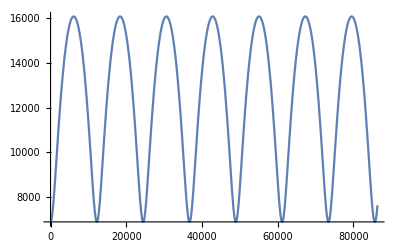

9702.43

6121.66

```mathematica
Subscript[m, satellite]=1000;
t0=0;
tf=86400;
G=6.674*10^-20;
Subscript[m, E]=5.972*10^24;
Subscript[r, E]=6371;



sol4=NDSolve[{rx''[t]== (-G*Subscript[m, E]*rx[t])/((rx[t]^2+ry[t]^2+rz[t]^2)^1.5),ry''[t]== (-G*Subscript[m, E]*ry[t])/((rx[t]^2+ry[t]^2+rz[t]^2)^1.5),rz''[t]== (-G*Subscript[m, E]*rz[t])/((rx[t]^2+ry[t]^2+rz[t]^2)^1.5),rx'[0]==-6.532,ry'[0]==0.7835,rz'[0]==6.142,rx[0]==3207,ry[0]==5459,rz[0]==2714},{rx,ry, rz},{t,t0,tf},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
rx[t_]=rx[t]/. sol4⟦1⟧;
ry[t_]=ry[t]/. sol4⟦1⟧;
rz[t_]=rz[t]/. sol4⟦1⟧;
R[t_]=Norm[{rx[t],ry[t],rz[t]}];
Plot[R[t],{t,t0,tf}]
res=FindMaximum[R[t],{t,0,5000}];
maxdistance=res⟦1⟧-Subscript[r, E] 
timerequired=(t/. res⟦2⟧)
```

## Problem 2.5

-Graphics-

```mathematica
ClearAll["Global`*"]
```

```mathematica
Subscript[m, satellite]=1000;
t0=0;
tf=86400;
G=6.674*10^-20;
Subscript[m, E]=5.972*10^24;
Subscript[r, E]=6371;
```

```mathematica
sol5=NDSolve[{rx''[t]== (-G*Subscript[m, E]*rx[t])/((rx[t]^2+ry[t]^2+rz[t]^2)^1.5),ry''[t]== (-G*Subscript[m, E]*ry[t])/((rx[t]^2+ry[t]^2+rz[t]^2)^1.5),rz''[t]== (-G*Subscript[m, E]*rz[t])/((rx[t]^2+ry[t]^2+rz[t]^2)^1.5),rx'[0]==0,ry'[0]==12,rz'[0]==0,rx[0]==6600,ry[0]==0,rz[0]==0},{rx,ry, rz,rx',ry', rz'},{t,t0,tf},Method->{"TimeIntegration"->"ExplicitRungeKutta"}];
Rx=Evaluate[rx[tf]/.sol5];
Ry=Evaluate[ry[tf]/.sol5];
Rz=Evaluate[rz[tf]/.sol5];
Vx=Evaluate[rx'[tf]/.sol5];
Vy=Evaluate[ry'[tf]/.sol5];
Vz=Evaluate[rz'[tf]/.sol5];
Dist=Norm[{Rx,Ry,Rz}]
V=Norm[{Vx,Vy,Vz}]
```

463259.

4.99415